```mathematica
ClearAll["Global`*"]
(*α=β+1/l^2*)
d[x_]=βoα+C1 Exp[−α^(1/2) x]+C2 Exp [α^(1/2) x];
sol=Solve[d[0]==1 && d'[1]==0,{C1,C2}]
```

{{C1→-(ⅇ^(2 √α) (-1+βoα))/(1+ⅇ^(2 √α)),C2→-(-1+βoα)/(1+ⅇ^(2 √α))}}

```mathematica
C1=C1/.sol[[1,1]]
C2=C2/.sol[[1,2]]
```

-(ⅇ^(2 √α) (-1+βoα))/(1+ⅇ^(2 √α))

-(-1+βoα)/(1+ⅇ^(2 √α))

```mathematica
(ⅇ^(2 √(1/l^2+β)))/((1+ⅇ^(2 √(1/l^2+β))) (1+l^2 β))
```

1/((1+ⅇ^(2 √(1/l^2+β))) (1+l^2 β))

```mathematica
ExpToTrig[C2]
```

1/((1+l^2 β) (1+Cosh[2 √(1/l^2+β)]+Sinh[2 √(1/l^2+β)]))

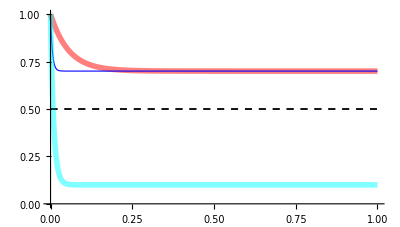

/Users/Kaushik/Google Drive/Career2016/Weilin/WFiles/broadening_mathematica_v2.pdf

```mathematica
pics=MapThread[Block[{l=#1,α=1/((1-#2 ) #1^2),βoα=#2},

ParametricPlot[{{x,d[x]},{x,0.5}},{x,0,1},PlotRange->{{0,1},{0,1}},
(*{l,2x}*)
AspectRatio->1/1.75,
ImageSize->Scaled[0.3],
PlotStyle->{#3,{Black,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}}]]&,{{0.1,0.01,0.01},{0.7,0.7,0.1},{{Red,Opacity[0.5],Thickness[0.01]},{Blue,Opacity[15],Thickness[0.002]},{Cyan,Opacity[0.5],Thickness[0.01]}}}];
P4 = Show[pics[[;;]]]
Export["/Users/Kaushik/Google Drive/Career2016/Weilin/WFiles/broadening_mathematica_v2.pdf",P4,"PDF"]
```

```mathematica
Block[{l=0.5},NSolve[(d[x]/.β->#)==0.95,x] &/@{1,5,50,100,200,500,1000}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve :: ifun will be suppressed during this calculation.

{{{x→ConditionalExpression[0.2 (0.0645448+(0.+6.28319 ⅈ) C[1]),C[1]∈Integers]},{x→ConditionalExpression[0.2 (9.93546+(0.+6.28319 ⅈ) C[1]),C[1]∈Integers]}},{{x→ConditionalExpression[0.111111 (0.119347+(0.+6.28319 ⅈ) C[1]),C[1]∈Integers]},{x→ConditionalExpression[0.111111 (17.8807+(0.+6.28319 ⅈ) C[1]),C[1]∈Integers]}},{{x→0.0208135}},{{x→0.0115767-0.0302076 ⅈ}},{{x→-0.00214831-0.0154 ⅈ}},{{x→-0.00330894-0.00623332 ⅈ}},{{x→-0.00243694-0.00312908 ⅈ}}}

```mathematica
d[x]
```

β/(1/l^2+β)+(ⅇ^(x (1/l^2+β)))/((1+ⅇ^(2/l^2+2 β)) (1+l^2 β))+(ⅇ^(2/l^2+x (-1/l^2-β)+2 β))/((1+ⅇ^(2/l^2+2 β)) (1+l^2 β))

E=160 Gpa
N[10^12/(2 160*10^9)]

E=160 Gpa
G_c= 3 J/m^2
σ_th=7 Gpa
ℓ=10 nm

.125

```mathematica
N[(3 *160*10^9)/((7 *10^9)^2)]
```

9.79592×10^-9